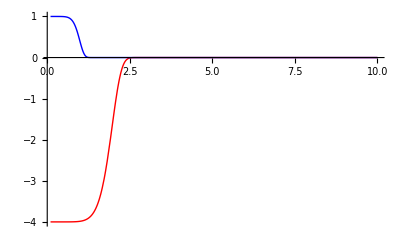

```mathematica
(*"Distance" units are measured as a function of the gel radius in the "off" state, i.e. 1u = 300 nm *)
(* Diffusion Coefficient is considered 1 here, hence this fix the time units *)
nm=1/300;
DiffCoeff = 1;
ns = nm^2/DiffCoeff;

VMax1=-4;
VMax2=1;
x0=0;
sigma1=600 nm;
sigma2=300 nm;
RSink =30 nm;
RMax=3000 nm;


k12=1.0;
k21=1.0;
tmax=200; (*200 is already ok to obtain convergence, check by plotting densities for tmax and tmax/2!*)

(* State 1 is the hydrophilic, extendend state, state 2 is the hydrophobic one. 
JAKOB, TO CHECK CONVERGENCE TO BOXCAR JUST USE DIFFERENT VALUES OF "enne", this is what I did to generate
the plot I sent you in the email!
 *)
enne=8;
Pot1[x_]:=VMax1 Exp[-((x-x0)/sigma1)^enne];
Pot2[x_]:=VMax2 Exp[-((x-x0)/sigma2)^enne];
Plot[{Pot1[x],Pot2[x]},{x,RSink,RMax},PlotStyle->{Red,Blue},PlotRange->All]
```

```mathematica
(* Parameters to generate T-dependet k12,k21 and Kr*)
DGstar=1000;
v0 = 500;
TLCS=300;
DS=-50;
v0Trans = 10;
DGthermo[T_]:=DS (T-TLCS);
DGkinetic=1000;
(* Densities is basically a list containing "functions" to be plotted, stored during the For cycle below
Densities[[i,1]]=rh01,[[i,2]]=rho2,[[i,3]]=rtot. i = 1/T
*)
Densities=Table[{0,0,0},{i,1,11}];
ReactionRate=Table[{0,0},{i,1,11}];
Densities2=Table[{0,0,0},{i,1,11}];
ReactionRate2=Table[{0,0},{i,1,11}];
SurfaceRate=Table[{0,0},{i,1,11}];

For[i=0,i<11,i++,
(* List of instructions *)
T=280 + i*5;
Ks=v0 Exp[-DGstar / T];
k12=v0Trans Exp[-(DGthermo[T]+DGkinetic)/T];
k21=v0Trans Exp[-(DGkinetic)/T];
sol=NDSolve[
{
Derivative[0,1][rho1][x,t]==2/x(Derivative[1,0][rho1][x,t]+rho1[x,t]Pot1'[x])+Derivative[2,0][rho1][x,t]+Derivative[1,0][rho1][x,t]Pot1'[x]+rho1[x,t]Pot1''[x]-k12 rho1[x,t]+k21 rho2[x,t],
Derivative[0,1][rho2][x,t]==2/x(Derivative[1,0][rho2][x,t]+rho2[x,t]Pot2'[x])+Derivative[2,0][rho2][x,t]+Derivative[1,0][rho2][x,t]Pot2'[x]+rho2[x,t]Pot2''[x]+k12 rho1[x,t]-k21 rho2[x,t],
rho1[x,0]==k21/(k12+k21)*(1-1/(1+Exp[10(x-RMax/2)])),
rho2[x,0]==k12/(k12+k21 )(1-1/(1+Exp[10(x-RMax/2)])),
rho1[RMax,t]==k21/(k12+k21),
rho2[RMax,t]==k12/(k12+k21),
4 π RSink^2 Derivative[1,0][rho1][RSink,t]==Ks rho1[RSink,t],
4 π RSink^2 Derivative[1,0][rho2][RSink,t]==Ks rho2[RSink,t]},
{rho1,rho2},
{x,RSink,RMax},{t,0,tmax},MaxSteps->Infinity,MaxStepFraction->0.002,AccuracyGoal->15,StartingStepSize->0.001,
Method->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->5000}}];
Print["DONE", T ];
r1[x_]:=rho1[x,tmax]/.sol;
r2[x_]:=rho2[x,tmax]/.sol;
rtot[x_]:=(rho1[x,tmax]+rho2[x,tmax])/.sol;

r1B[x_]:=rho1[x,tmax/2]/.sol;
r2B[x_]:=rho2[x,tmax/2]/.sol;
rtotB[x_]:=(rho1[x,tmax/2]+rho2[x,tmax/2])/.sol;


Densities[[i+1,1]]=r1[x];
Densities[[i+1,2]]=r2[x];
Densities[[i+1,3]]=rtot[x];

Densities2[[i+1,1]]=r1B[x];
Densities2[[i+1,2]]=r2B[x];
Densities2[[i+1,3]]=rtotB[x];

ReactionRate[[i+1,1]]=1/T;
ReactionRate[[i+1,2]]=Ks rtot[RSink];

ReactionRate2[[i+1,1]]=1/T;
ReactionRate2[[i+1,2]]=Ks rtotB[RSink];


SurfaceRate[[i+1,1]]=1/T;
SurfaceRate[[i+1,2]]=Ks
]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

DONE280

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

DONE285

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

General::stop: Further output of NDSolve :: mxsst will be suppressed during this calculation.

DONE290

DONE295

DONE300

DONE305

DONE310

DONE315

DONE320

DONE325

DONE330

{1.47148}

{1.2781}

{1.00538}

{0.663208}

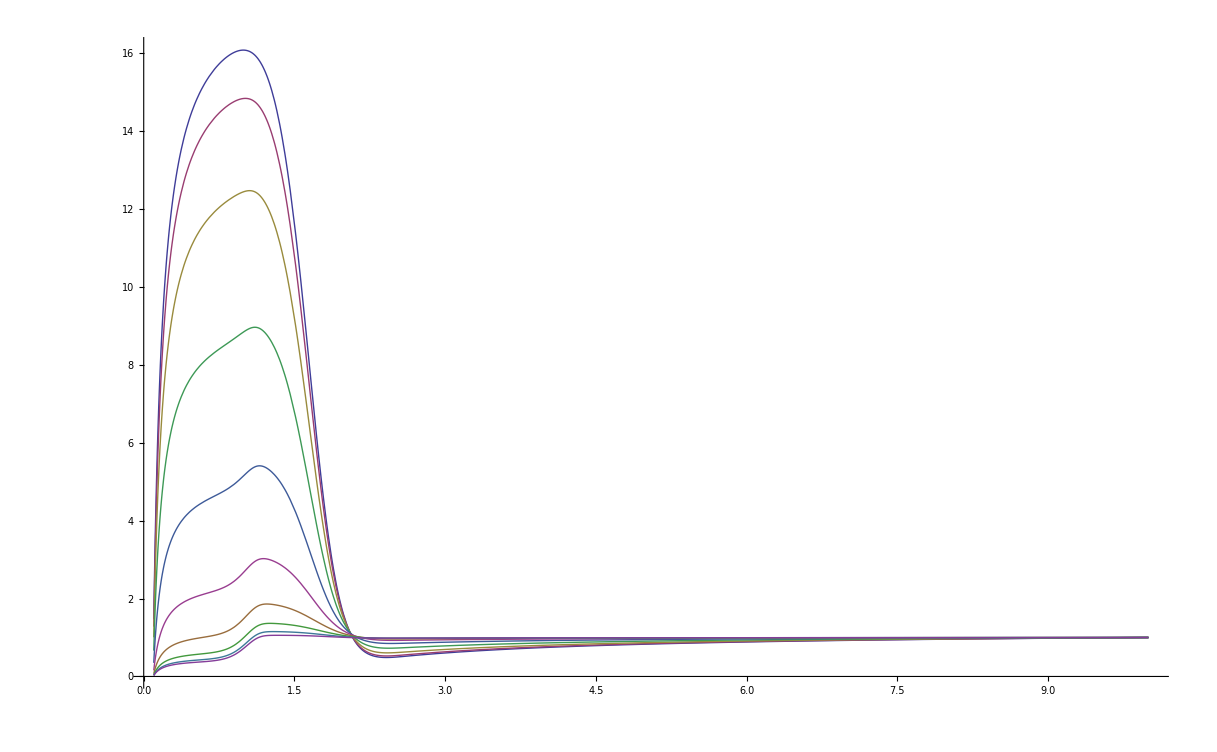

```mathematica
Densities[[1,3]]/.x->RSink
Densities[[2,3]]/.x->RSink
Densities[[3,3]]/.x->RSink
Densities[[4,3]]/.x->RSink

Plot[{Densities[[1,3]],
Densities[[2,3]],
Densities[[3,3]],
Densities[[4,3]],
Densities[[5,3]],
Densities[[6,3]],
Densities[[7,3]],
Densities[[8,3]],
Densities[[9,3]],
Densities[[10,3]]},{x,RSink,RMax},PlotRange->All]
```

{{0.00357143,20.6858},{0.00350877,19.1291},{0.00344828,15.9857},{0.00338983,11.1798},{0.00333333,6.22916},{0.00327869,2.93838},{0.00322581,1.40144},{0.0031746,0.813848},{0.003125,0.604437},{0.00307692,0.528264},{0.0030303,0.498362}}

{{0.00357143,14.0578},{0.00350877,14.9668},{0.00344828,15.9002},{0.00338983,16.8572},{0.00333333,17.837},{0.00327869,18.8388},{0.00322581,19.8619},{0.0031746,20.9053},{0.003125,21.9685},{0.00307692,23.0504},{0.0030303,24.1505}}

{-43.8742,-68.7846,-2973.74,33.1951,9.57195,3.48139,1.50784,0.846815,0.621538,0.540654,0.508863}

{0.00357143,0.00350877,0.00344828,0.00338983,0.00333333,0.00327869,0.00322581,0.0031746,0.003125,0.00307692,0.0030303}

{{0.00357143,-43.8742},{0.00350877,-68.7846},{0.00344828,-2973.74},{0.00338983,33.1951},{0.00333333,9.57195},{0.00327869,3.48139},{0.00322581,1.50784},{0.0031746,0.846815},{0.003125,0.621538},{0.00307692,0.540654},{0.0030303,0.508863}}

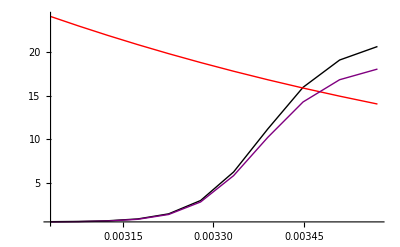

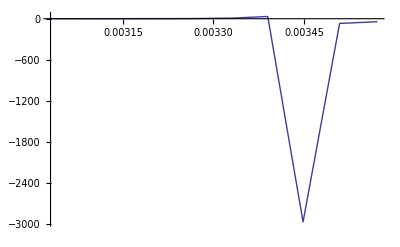

```mathematica
a=N[Partition[Flatten[ReactionRate],2]]
b=N[Partition[Flatten[SurfaceRate],2]]

a2=Partition[Flatten[ReactionRate2],2];


c=a[[All,2]]b[[All,2]]/(b[[All,2]]-a[[All,2]])
cc=b[[All,1]]
d = Transpose[{cc,c}]

ListPlot[{a,b,a2},Joined->True,PlotRange->All,PlotStyle->{Black,Red,Purple}]
ListPlot[{d},Joined->True,PlotRange->All]
```